```mathematica
SetDirectory[NotebookDirectory[]];
countryWideConfirmed=Import["./COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv","CSV"];
```

```mathematica
countryWideConfirmedExChina = DeleteCases[countryWideConfirmed,{_,"China",__}];
countryWideConfirmedExChina=Drop[countryWideConfirmedExChina,1,{1,4}];
globalConfirmedExChina = Transpose[{Total[countryWideConfirmedExChina,{1}]}];
dataGlobal=MapThread[Prepend,{globalConfirmedExChina,Table[a,{a,0,Length[globalConfirmedExChina]-1,1}]}]

confirmedUS = Cases[countryWideConfirmed,{_,"US",__}];
confirmedUS=Transpose[Drop[confirmedUS,0,{1,4}]];
dataUS=MapThread[Prepend,{confirmedUS,Table[a,{a,0,Length[confirmedUS]-1,1}]}]
```

{{0,7},{1,11},{2,21},{3,28},{4,43},{5,50},{6,69},{7,79},{8,93},{9,125},{10,147},{11,157},{12,165},{13,185},{14,195},{15,207},{16,281},{17,306},{18,321},{19,408},{20,416},{21,462},{22,473},{23,527},{24,617},{25,711},{26,824},{27,925},{28,1020},{29,1120},{30,1269},{31,1571},{32,1936},{33,2320},{34,2652},{35,3222},{36,4146},{37,5184},{38,6655},{39,8437},{40,10170},{41,12579},{42,14734},{43,17349},{44,21111},{45,25077},{46,28998},{47,32730},{48,37733},{49,44954},{50,47420},{51,64260},{52,75124},{53,86451},{54,100541},{55,116044},{56,133719},{57,161344},{58,190785},{59,223091},{60,255518},{61,296737},{62,336454},{63,385992},{64,447809},{65,511394},{66,578707},{67,637995},{68,700167},{69,775208},{70,850244},{71,930725},{72,1013406},{73,1114862}}

{{0,1},{1,1},{2,2},{3,2},{4,5},{5,5},{6,5},{7,5},{8,5},{9,7},{10,8},{11,8},{12,11},{13,11},{14,11},{15,11},{16,11},{17,11},{18,11},{19,11},{20,12},{21,12},{22,13},{23,13},{24,13},{25,13},{26,13},{27,13},{28,13},{29,13},{30,15},{31,15},{32,15},{33,51},{34,51},{35,57},{36,58},{37,60},{38,68},{39,74},{40,98},{41,118},{42,149},{43,217},{44,262},{45,402},{46,518},{47,583},{48,959},{49,1281},{50,1663},{51,2179},{52,2727},{53,3499},{54,4632},{55,6421},{56,7783},{57,13677},{58,19100},{59,25489},{60,33276},{61,43847},{62,53740},{63,65778},{64,83836},{65,101657},{66,121478},{67,140886},{68,161807},{69,188172},{70,213372},{71,243453},{72,275586},{73,308850}}

```mathematica
lessFancyModel[r_?NumberQ,k_?NumberQ,p_?NumberQ,c0_?NumberQ]:=Module[{c,t},First[c/.NDSolve[{c'[t]==r*c[t]^p*(1-(c[t]/k)),c[0]==c0},c,{t,0,110}]]]
fancyFitUS=NonlinearModelFit[dataUS,{lessFancyModel[r,k,p,c0][t]},{{r,.2},k,p,c0},t]
fancyFitUS["ParameterConfidenceIntervalTable"]
fancyFitUS["RSquared"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[InterpolatingFunction[{{0., 110.}}, <>][t]]

| Estimate | Standard Error | Confidence Interval
r | 0.330146 | 0.108526 | {0.113697,0.546594}
k | 506963. | 32208.1 | {442726.,571200.}
p | 0.970391 | 0.0303017 | {0.909956,1.03083}
c0 | 0.000209292 | 0.00144782 | {-0.00267829,0.00309687}

0.999434

| Estimate | Standard Error | Confidence Interval
a | 496.884 | 0.000475866 | {496.883,496.885}
b | 0.240283 | 0.00410061 | {0.232104,0.248461}
c | 478593. | 13544.3 | {451580.,505606.}
d | 10.7832 | 0.236449 | {10.3116,11.2548}

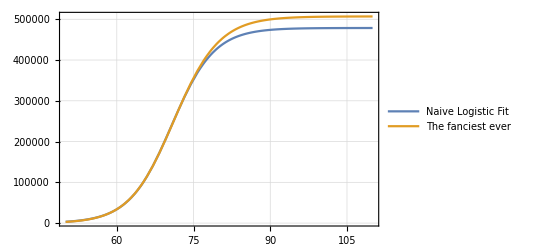

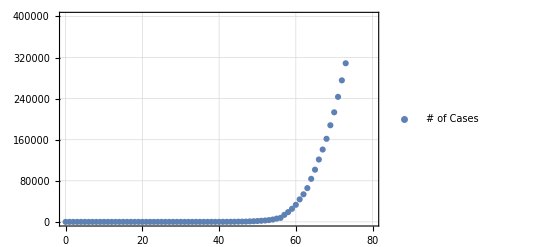

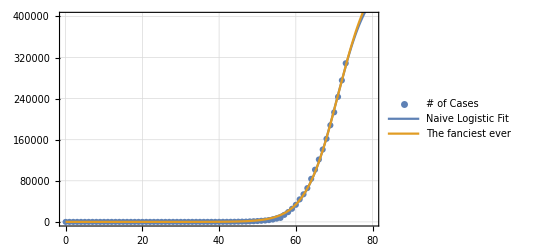

```mathematica
fitLogUS=NonlinearModelFit[dataUS,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
fitLogUS["ParameterConfidenceIntervalTable"]
Plot[{Normal[fitLogUS],Normal[fancyFitUS]},{t,50,110},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"},Frame->True,GridLines->Automatic]
scatterPlotUS=ListPlot[dataUS,PlotRange->{{0,80},{0,400000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlotsUS=Plot[{Normal[fitLogUS],Normal[fancyFitUS]},{t,0,100},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"}];
Show[scatterPlotUS,fitPlotsUS]
```

```mathematica
fancyModel[r_?NumberQ,k_?NumberQ,p_?NumberQ,c0_?NumberQ]:=Module[{c,t},First[c/.NDSolve[{c'[t]==r*c[t]^p*(1-(c[t]/k)),c[0]==c0},c,{t,0,110}]]]
fancyFitGlobal=NonlinearModelFit[dataGlobal,{fancyModel[r,k,p,c0][t]},{{r,.2},k,p,c0},t]
fancyFitGlobal["ParameterConfidenceIntervalTable"]
fancyFitGlobal["RSquared"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[InterpolatingFunction[{{0., 110.}}, <>][t]]

| Estimate | Standard Error | Confidence Interval
r | 0.297821 | 0.0552182 | {0.187692,0.40795}
k | 2.14217×10^6 | 96782.4 | {1.94915×10^6,2.3352×10^6}
p | 0.951939 | 0.0153961 | {0.921233,0.982646}
c0 | 0.551964 | 0.843693 | {-1.13073,2.23466}

0.999863

(1.91165×10^6)/(1+85.7339 ⅇ^(7.42692-0.166825 t))

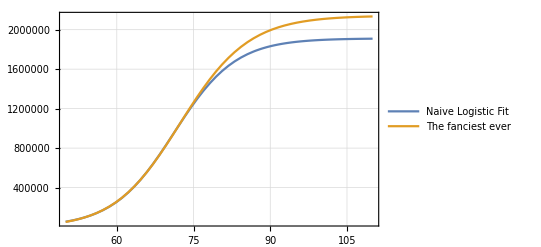

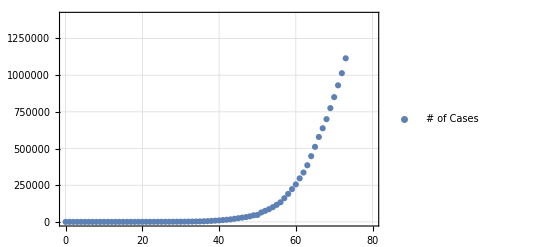

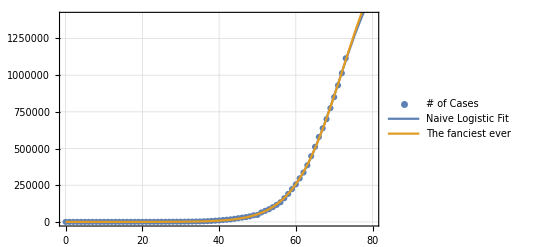

```mathematica
fitLogGlobal=NonlinearModelFit[dataGlobal,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
Normal[fitLogGlobal]
Plot[{Normal[fitLogGlobal],Normal[fancyFitGlobal]},{t,50,110},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"},Frame->True,GridLines->Automatic]
scatterPlotGlobal=ListPlot[dataGlobal,PlotRange->{{0,80},{0,1400000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlotsGlobal=Plot[{Normal[fitLogGlobal],Normal[fancyFitGlobal]},{t,0,100},PlotRange->All,PlotLegends->{"Naive Logistic Fit","The fanciest ever"}];
Show[scatterPlotGlobal,fitPlotsGlobal]
```